# Mathematica Functions Lab #1

## Part I: How much space in the box?

Imagine you have a box.  It has height, width, and length, with variables as appropriate.  You wish to determine the volume (V) of this box, shown below in Figure 1.  The mathematical model for this is:

V = l × h × w

This is a simple equation to determine.  However, as a mathematical model, it’s wrong.  Why?  It’s wrong because there is actually some loss of volume because the walls of the box have some thickness, and that thickness takes up some of the volume of the box.  The improved mathematical model is:

V = (h-2t)×(w-2t)×(l-2t)

In this case, t is the thickness of the walls.  For all of the problems here, all of our measurements are in units of centimeters (cm).

-Graphics-
Figure 1:  Volume of a box | ()

### Lab Activity:

#### Build a model that determines the volume of a box that has a length of 200 cm, a width of 300 cm, and a height of 400 cm. The FUNCTION name should be: volumeNoWalls. Calculate the volume with these dimensions. REMEMBER that in Mathematica, you use a space to represent multiplication, not an “x” or a “*”. Your function should have THREE parameters. When you USE the function, make sure the answer has a variable name! For example: simpleVolume = volumeNoWalls[length, width, height].

```mathematica
volumeNoWalls[l_, w_, h_] := l w h
```

```mathematica
l = 200;
w=300;
h=400;
```

```mathematica
simpleVolume = volumeNoWalls[l, w, h]
```

24000000

#### Build a model that determines the volume of the box with the same dimensions but with a wall thickness of 5 cm. Calculate the volume with the same dimensions AND thickness = 5 cm. The FUNCTION name should be: volumeWithWalls. Your function should have FOUR parameters. When you USE the function, make sure you give this volume a variable name. For example, if the wall thickness was 5 cm, I would use something like “volume5cm”, for example: volume5cm = volumeWithWalls[...]

```mathematica
volumeWithWalls[l_, w_, h_, t_]:= (h-2 t) (w-2 t) (l-2t)
```

```mathematica
l=200;
w = 300;
h=400;
t=5;
```

```mathematica
volume5cm = volumeWithWalls[l,w,h,t]
```

21489000

#### Build a “comparison checker” (it’s the same formula as percent error). In this equation, you are determining by what percentage two values are different. The two sticks (“|”) are, if you don’t recognize them, the mathematical symbols for absolute value. REMEMBER that you never use ANY symbols for multiplication (x, *) -- you use a space! The “lower of the two values” means you find the MINIMUM of first value and second value.

percent difference = (| first value - second value |)/(lower of the two values) x 100

```mathematica
percentDifference[val1_, val2_] := Abs[val1-val2]/Min[val1,val2]  100
```

#### Now, calculate the percent difference between the two volumes (the box with wall thicknesses that are “zero” (impossible!) and the box with a 5 cm thick wall).

```mathematica
volumeDiff = N[percentDifference[simpleVolume,volume5cm]]
```

11.685

#### What does your data suggest about the this assumption that the first box has walls with no thickness? Is is this a good assumption? If the percent difference is more than a small percentage -- like more than 5% -- then this is probably not a very good model.

TYPE YOUR ANSWER AFTER THIS LINE:  THe difference is more than 5% which means that there is a significant difference in volume when analyzing the thickness of the walls of the box.

#### Calculate the volume of two boxes, one with a wall thickness of 5 cm and one with a thickness of 4 cm. Determine the percent difference. How do these two models compare?

```mathematica
t=4;
volume4cm = volumeWithWalls[l,w,h,t];
N[percentDifference[volume5cm,volume4cm]]
```

2.27134

TYPE YOUR ANSWER AFTER THIS LINE: These models percent difference is less than 5% which means that there isn’t a super big difference in volume.

#### Build a data table where you determine volumes for wall thicknesses going from 0 to 10 cm. Plot this data. Describe the graph.

```mathematica
results = Table[
{
t,
volumeWithWalls[l,w,h,t]
},
{t,1,10}
]
```

{{1,23483592},{2,22974336},{3,22472184},{4,21977088},{5,21489000},{6,21007872},{7,20533656},{8,20066304},{9,19605768},{10,19152000}}

```mathematica
Grid[Prepend[results,{"t","volume"}], Frame -> All]
```

t | volume
1 | 23483592
2 | 22974336
3 | 22472184
4 | 21977088
5 | 21489000
6 | 21007872
7 | 20533656
8 | 20066304
9 | 19605768
10 | 19152000

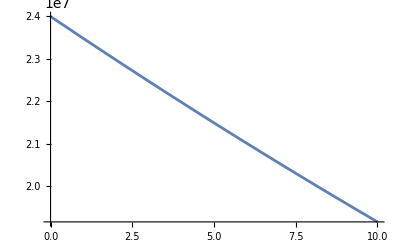

```mathematica
Plot[volumeWithWalls[l,w,h,t],{t,0,10}]
```

#### Perform a linear regression of this dataset. What do you find as the value of the slope?

```mathematica
reg=Fit[results,{1,x},x]
```

2.3923×10^7-481243. x

## Part II: The Logistic Model

### Description:

One of the more common models/algorithms found in computational science is the logistic function.  This model is primarily used to model population growth of an organism over some period of time.  The equation is:

ΔP = (P_0 M)/((M - P_0) e^(-r t) + P_0)

where P is the initial population (starting number of organisms), M is the carrying capacity (the maximum number of organisms that the environment can contain), r is the growth rate (provided as a percentage), and t is time.  
Notice that this is an exponential function, meaning that the results will typically have a curved shape when you plot them.

### Lab Activity:

#### Plot the logistic function with initial population P_0 = 20, carrying capacity M = 1000, and instantaneous rate of change of births r = 50% = 0.5 from t = 0 to t = 16 to obtain a graph.

```mathematica
dP[P0_, M_, r_, t_] :=(P0 M)/((M - P0) E^(-r t)+P0);
```

```mathematica
P0 = 20;
M = 1000;
r = 0.5;
```

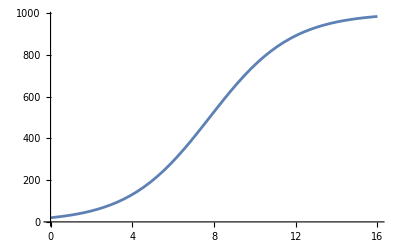

```mathematica
Plot[dP[P0,M,r,t],{t,0,16}]
```

#### On the same graph in red, green, and blue, respectively, plot three logistic functions that each have M =1000 and r = 0.5 but P_0 values of 20, 100, and 200.

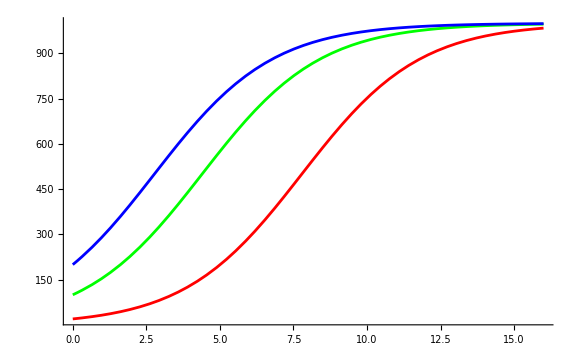

```mathematica
P01 = 20;
P02 = 100;
P03 = 200;
p1 = Plot[dP[P01,M,r,t],{t,0,16}, PlotRange -> All, PlotStyle -> Red];
p2 = Plot[dP[P02,M,r,t],{t,0,16},PlotRange-> All, PlotStyle -> Green];
p3 = Plot[dP[P03,M,r,t],{t,0,16},PlotRange-> All,PlotStyle-> Blue];
Show[p1,p2,p3,PlotRange->All,ImageSize-> Large]
```

#### What effect does P_0 have on a logistic graph?

TYPE YOUR ANSWER AFTER THIS LINE: It’s the starting population size and makes the graph more stretched.

#### On the same graph, plot three logistic functions that each have M =1000 and P_0=20 but r values of 0.2, 0.5, and 0.8.

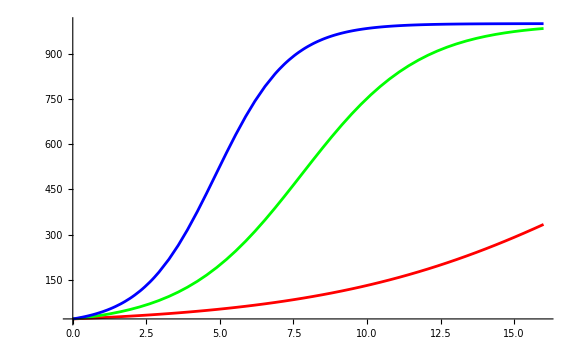

```mathematica
r1 = 0.2;
r2 = 0.5;
r3 = 0.8;
p1 = Plot[dP[P0,M,r1,t],{t,0,16}, PlotRange -> All, PlotStyle -> Red];
p2 = Plot[dP[P0,M,r2,t],{t,0,16},PlotRange-> All, PlotStyle -> Green];
p3 = Plot[dP[P0,M,r3,t],{t,0,16},PlotRange-> All,PlotStyle-> Blue];
Show[p1,p2,p3,PlotRange->All,ImageSize-> Large]
```

#### What effect does r have on a logistic graph?

TYPE YOUR ANSWER AFTER THIS LINE: A higher r value means a more rapid rate of change and more steep slope.

#### On the same graph in red, green, and blue, respectively, plot three logistic functions that each have P_0 = 20 and r = 0.5 but M values of 1000, 1300, and 2000.

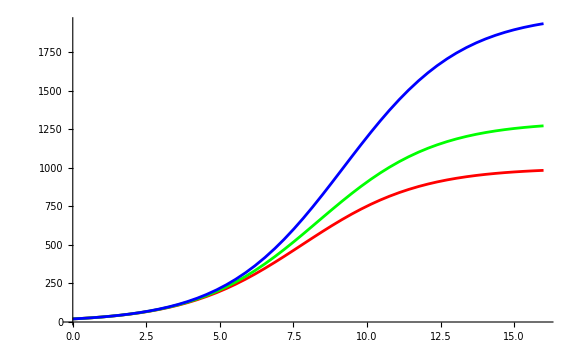

```mathematica
M1 = 1000;
M2 = 1300;
M3 = 2000;
p1 = Plot[dP[P0,M1,r,t],{t,0,16}, PlotRange -> All, PlotStyle -> Red];
p2 = Plot[dP[P0,M2,r,t],{t,0,16},PlotRange-> All, PlotStyle -> Green];
p3 = Plot[dP[P0,M3,r,t],{t,0,16},PlotRange-> All,PlotStyle-> Blue];
Show[p1,p2,p3,PlotRange->All,ImageSize-> Large]
```

#### What effect does M have on a logistic graph?

TYPE YOUR ANSWER AFTER THIS LINE: It serves as an asymptote and determines the maximum value that the graph could reach.